```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Lion\Documents\My Projects\GOT\Extract txt

```mathematica
FileNames[]
```

{6pgames_old.txt,6pgames.txt,Castles,Castles.nb,Dectract.py,Extract.py,Fights,Fights.nb,GetCastles.py,GetFights.py,GetHTML.py,GetNumbers.py,GetOpenings.py,GetWinners.py,htmls,nr.txt,Numbers,Openings,Openings.nb,Openingsstark.png,OpeningStark_old.txt,ratedgames.txt,RatedvsUnrated.nb,Scraper.py,S.m,Winners.nb,winners.txt}

```mathematica
allgames=Import["6pgames.txt","Table","FieldSeparators"->","];
```

```mathematica
ratedgames=Transpose[Cases[allgames,{_Integer,_String,_,"rated"}]][[1]];
unratedgames=Transpose[Cases[allgames,{_Integer,_String,_,"unrated"}]][[1]];
```

```mathematica
Length[ratedgames]
Length[unratedgames]
```

5377

2900

```mathematica
Length[allgames]
```

8277

```mathematica
games2winners[pos_]:=games2winners[pos]=(
SetDirectory["C:\\Users\\Lion\\Documents\\My Projects\\GOT\\Extract txt"];
winners=Import["winners.txt","Table","FieldSeparators"->","];
winners2=Cases[winners,{#,_String}][[1,2]]&/@pos;
names={"Lennister","Martell","Tyrell","Graufreud","Stark","Baratheon"};
namesen={"Lannister","Martell","Tyrell","Greyjoy","Stark","Baratheon"};
rate=Table[Count[winners2,names[[i]]],{i,1,Length[names]}];
BarChart[rate/Total[rate]*100.,ChartLabels->namesen,ChartStyle->{RGBColor[{0.9,0,0}], Orange, RGBColor[{0,0.7,0}], Black,White,Yellow},PlotLabel->StringForm["From `` Games",Length[winners2]],Frame->True,FrameLabel->{None,"Winrate [%]"},ImageSize->Large]
)
```

```mathematica
Needs["ErrorBarPlots`"]
Clear[games2castles]
games2castles[pos_]:=games2castles[pos]=(
SetDirectory["C:\\Users\\Lion\\Documents\\My Projects\\GOT\\Extract txt\\Castles"];
castles=<<"EndCastles.txt";
castlesmean=Mean[Cases[castles,{#,_Integer,_Integer,_Integer,_Integer,_Integer,_Integer}][[1,2;;7]]&/@pos];
castlesdev=StandardDeviation[Cases[castles,{#,_Integer,_Integer,_Integer,_Integer,_Integer,_Integer}][[1,2;;7]]&/@pos];
names={"Lennister","Martell","Tyrell","Graufreud","Stark","Baratheon"};
namesen={"Lannister","Martell","Tyrell","Greyjoy","Stark","Baratheon"};
mean=Flatten[Transpose[{castlesmean}]];
Show[BarChart[mean,ChartLabels->namesen,ChartStyle->{RGBColor[{0.9,0,0}], Orange, RGBColor[{0,0.7,0}], Black,White,Yellow},PlotLabel->StringForm["From `` Games",Length[pos]],Frame->True,FrameLabel->{None,"#Castles"},ImageSize->Large],ErrorListPlot[Transpose[{castlesmean,castlesdev}],PlotRange->{Automatic,{0,7}},PlotStyle->{Dashed,Gray}]]
)
```

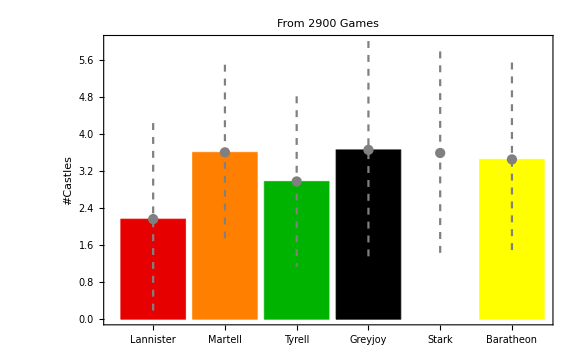

```mathematica
games2castles[unratedgames]
```

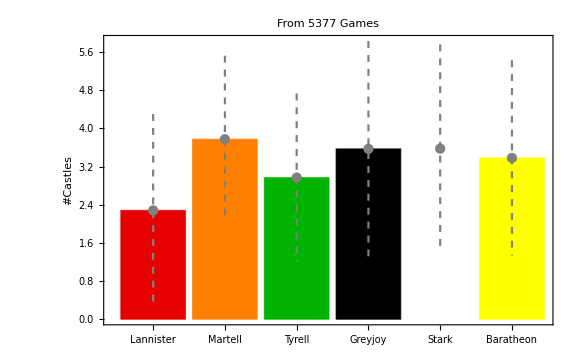

```mathematica
games2castles[ratedgames]
```